```mathematica
Goldstein & Price
```

Price (Goldstein&)

```mathematica
f[xx_,yy_]:=(1+(xx+yy+1)^2*(19-14*xx+3*xx^2-14*yy+6*xx*yy+3*yy^2))*(30+(2*xx-3*yy)^2*(18-32*xx+12*xx^2+48*yy-36*xx*yy+27*yy^2))
```

```mathematica
Plot3D[f[xx,yy],{xx,-2,2},{yy,-2,2}]
```

-Graphics3D-

```mathematica
f[2,2]
```

76728

```mathematica
D[f[xx,yy],xx]//FullSimplify
```

24 (-1+2 xx-3 yy) (2 xx-3 yy) (2 xx-3 (1+yy)) (1+(1+xx+yy)^2 (19+3 xx^2+yy (-14+3 yy)+2 xx (-7+3 yy)))+12 (-2+xx+yy) (-1+xx+yy) (1+xx+yy) (30+(2 xx-3 yy)^2 (12 xx^2-4 xx (8+9 yy)+3 (6+yy (16+9 yy))))

```mathematica
D[f[xx,yy],yy]//FullSimplify
```

-36 (-1+2 xx-3 yy) (2 xx-3 yy) (2 xx-3 (1+yy)) (1+(1+xx+yy)^2 (19+3 xx^2+yy (-14+3 yy)+2 xx (-7+3 yy)))+12 (-2+xx+yy) (-1+xx+yy) (1+xx+yy) (30+(2 xx-3 yy)^2 (12 xx^2-4 xx (8+9 yy)+3 (6+yy (16+9 yy))))

```mathematica
Branin (rcos)
```

Branin rcos

```mathematica
br[xx_,yy_]:=a*(yy-b*xx^2+c*xx-d)^2+e*(1-f)*Cos[xx]+e /.{a->1,b->5.1/(4*π^2),c->5/π,d->6,e->10,f->1/(8*π)}
```

```mathematica
Plot3D[br[xx,yy],{xx,-5,10},{yy,0,15}]
```

-Graphics3D-

```mathematica
D[br[xx,yy],xx]
```

2 (5/π-0.258369 xx) (-6+(5 xx)/π-0.129185 xx^2+yy)-10 (1-1/(8 π)) Sin[xx]

```mathematica
D[br[xx,yy],yy]
```

2 (-6+(5 xx)/π-0.129185 xx^2+yy)

```mathematica
Six-Hump camel back
```

-back camel Hump+Six

```mathematica
sh[xx_,yy_]:=(4-2.1*xx^2+xx^4/3)*xx^2+xx*yy+(-4+4*yy^2)*yy^2
```

```mathematica
Plot3D[sh[xx,yy],{xx,-2,2},{yy,-1,1}]
```

-Graphics3D-

```mathematica
D[sh[xx,yy],xx]
```

xx^2 (-4.2 xx+(4 xx^3)/3)+2 xx (4-2.1 xx^2+xx^4/3)+yy

```mathematica
D[sh[xx,yy],yy]
```

xx+8 yy^3+2 yy (-4+4 yy^2)

```mathematica
Peaks
```

Peaks

```mathematica
p[xx_,yy_]:=3(1-xx)^2*Exp[-xx^2-(yy+1)^2]-10*(xx/5-xx^3-yy^5)*Exp[-xx^2-yy^2]-1/3*Exp[-(xx+1)^2-yy^2]
```

```mathematica
Plot3D[p[xx,yy],{xx,-4,4},{yy,-3,3}]
```

-Graphics3D-

```mathematica
dp1[x_,y_]=D[p[x,y],x]
dp2[x_,y_]=D[p[x,y],y]
```

-6 ⅇ^(-x^2-(1+y)^2) (1-x)-6 ⅇ^(-x^2-(1+y)^2) (1-x)^2 x+2/3 ⅇ^(-(1+x)^2-y^2) (1+x)-10 ⅇ^(-x^2-y^2) (1/5-3 x^2)+20 ⅇ^(-x^2-y^2) x (x/5-x^3-y^5)

2/3 ⅇ^(-(1+x)^2-y^2) y+50 ⅇ^(-x^2-y^2) y^4-6 ⅇ^(-x^2-(1+y)^2) (1-x)^2 (1+y)+20 ⅇ^(-x^2-y^2) y (x/5-x^3-y^5)

```mathematica
Plot3D[dp1[xx,yy],{xx,-3,3},{yy,-3,3}]
Plot3D[dp2[xx,yy],{xx,-3,3},{yy,-3,3}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Solve[{dp1[x,y]==0,dp2[x,y]==0},{x,y}]
```

$Aborted

```mathematica
FindRoot[{dp1[x,y]==0,dp2[x,y]==0},{{x,0},{y,-2}}]
FindRoot[{dp1[x,y]==0,dp2[x,y]==0},{{x,0},{y,0}}]
```

{x→0.416323,y→-0.394145}

{x→-0.265938,y→0.46674}

```mathematica
dp1[x,y]//Simplify
```

-2/3 ⅇ^(-2 x-x^2-(1+y)^2) (-ⅇ^(2 y) (1+x)+9 ⅇ^(2 x) (1-2 x^2+x^3)+ⅇ^(1+2 x+2 y) (3-51 x^2+30 x^4+30 x y^5))

```mathematica
Ackley
```

```mathematica
a=20;b=0.2;c=2*Pi;
```

```mathematica
norme[xx_,yy_]:=Sqrt[xx^2+yy^2]
```

```mathematica
ex1[xx_,yy_]:=Exp[-b*norme[xx,yy]/Sqrt[2]]
sco[xx_,yy_]:=Cos[c*xx]+Cos[c*yy]
ex2[xx_,yy_]:=Exp[sco[xx,yy]/2]
```

```mathematica
p[xx_,yy_]:=-a*ex1[xx,yy]-ex2[xx,yy]+Exp[1]
```

```mathematica
p[x,y]
```

ⅇ-20 ⅇ^(-0.141421 √(x^2+y^2))-ⅇ^(1/2 (Cos[2 π x]+Cos[2 π y]))

```mathematica
Plot3D[p[xx,yy],{xx,-2,2},{yy,-2,2}]
```

-Graphics3D-

```mathematica
dp1[x_,y_]:=D[p[x,y],x]
dp2[x_,y_]:=D[p[x,y],y]
dp1[x,y]
dp2[x,y]
```

(2.82843 ⅇ^(-0.141421 √(x^2+y^2)) x)/(√(x^2+y^2))+ⅇ^(1/2 (Cos[2 π x]+Cos[2 π y])) π Sin[2 π x]

(2.82843 ⅇ^(-0.141421 √(x^2+y^2)) y)/(√(x^2+y^2))+ⅇ^(1/2 (Cos[2 π x]+Cos[2 π y])) π Sin[2 π y]

```mathematica
Solve[{dp1[x,y]==0,dp2[x,y]==0},{x,y}]
```

$Aborted

```mathematica
Plot3D[dp1[xx,yy],{xx,-2,2},{yy,-2,2}]
Plot3D[dp2[xx,yy],{xx,-2,2},{yy,-2,2}]
```

General::ivar: -1.99971 is not a valid variable.

General::ivar: -1.714 is not a valid variable.

General::ivar: -1.42829 is not a valid variable.

General::stop: Further output of General will be suppressed during this calculation.

-Graphics3D-

General::ivar: -1.99971 is not a valid variable.

General::stop: Further output of General will be suppressed during this calculation.

-Graphics3D-

```mathematica
AHE (Axis parallel Hyper-Ellipsoid // Weighted Sphere Model)
```

```mathematica
p[xx_,yy_]:=xx^2+yy^2
```

```mathematica
dp1[x_,y_]:=D[p[x,y],x]
dp2[x_,y_]:=D[p[x,y],y]
dp1[x,y]
dp2[x,y]
```

2 x

2 y

```mathematica
Plot3D[p[xx,yy],{xx,-5.12,5.12},{yy,-5.12,5.12}]
```

-Graphics3D-

```mathematica
Beale
```

```mathematica
p[xx_,yy_]:=(1.5-xx+xx*yy)^2+(2.25-xx+xx*yy^2)^2+(2.625-xx+xx*yy^3)^2
```

```mathematica
dp1[x_,y_]:=D[p[x,y],x]
dp2[x_,y_]:=D[p[x,y],y]
dp1[x,y]
dp2[x,y]
```

2 (-1+y) (1.5-x+x y)+2 (-1+y^2) (2.25-x+x y^2)+2 (-1+y^3) (2.625-x+x y^3)

2 x (1.5-x+x y)+4 x y (2.25-x+x y^2)+6 x y^2 (2.625-x+x y^3)

```mathematica
Plot3D[p[xx,yy],{xx,-4.5,4.5},{yy,-4.5,4.5}]
```

-Graphics3D-

```mathematica
Solve[{dp1[x,y]==0,dp2[x,y]==0},{x,y}]
```

{{x→0.,y→1.},{x→0.-3.91038×10^-16 ⅈ,y→-0.928571+1.25153 ⅈ},{x→0.+3.91038×10^-16 ⅈ,y→-0.928571-1.25153 ⅈ},{x→0.100538,y→-2.64451},{x→1.9668-0.428576 ⅈ,y→-0.511077-0.607484 ⅈ},{x→1.9668+0.428576 ⅈ,y→-0.511077+0.607484 ⅈ},{x→3.,y→0.5}}

```mathematica
Bohachevski 1
```

```mathematica
p[xx_,yy_]:=xx^2+2*yy^2-0.3*Cos[3*Pi*xx]-0.4*Cos[4*Pi*yy]+0.7
```

```mathematica
dp1[x_,y_]:=D[p[x,y],x]
dp2[x_,y_]:=D[p[x,y],y]
dp1[x,y]
dp2[x,y]
```

2 x+2.82743 Sin[3 π x]

4 y+5.02655 Sin[4 π y]

```mathematica
borne=100;
```

```mathematica
Plot3D[p[xx,yy],{xx,-borne,borne},{yy,-borne,borne}]
```

-Graphics3D-

```mathematica
Plot3D[dp1[xx,yy],{xx,-2,2},{yy,-2,2}]
Plot3D[dp2[xx,yy],{xx,-2,2},{yy,-2,2}]
```

General::ivar: -1.99971 is not a valid variable.

General::ivar: -1.714 is not a valid variable.

General::ivar: -1.42829 is not a valid variable.

General::stop: Further output of General will be suppressed during this calculation.

-Graphics3D-

General::ivar: -1.99971 is not a valid variable.

General::stop: Further output of General will be suppressed during this calculation.

-Graphics3D-

```mathematica
Solve[{dp1[x,y]==0,dp2[x,y]==0},{x,y}]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[{2 x+2.82743 Sin[3 π x]==0,4 y+5.02655 Sin[4 π y]==0},{x,y}]

```mathematica
Fonctions 1D
```

```mathematica
p[xx_]:=15*Cos[xx]+20
```

```mathematica
dp[xx_]=D[p[xx],xx]
```

-15 Sin[xx]

```mathematica
p[x]
```

20+15 Cos[x]

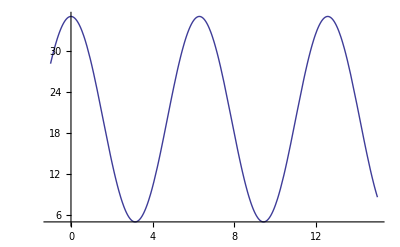

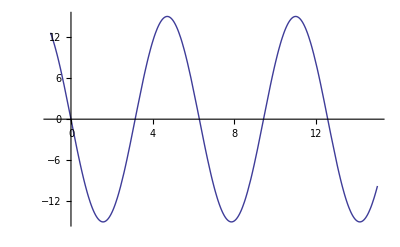

```mathematica
Plot[p[x],{x,-1,15}]
Plot[dp[x],{x,-1,15}]
```

```mathematica
p[xx_]:=Cos[4*xx]
```

```mathematica
dp[xx_]=D[p[xx],xx]
```

-4 Sin[4 xx]

```mathematica
p[x]
```

Cos[4 x]

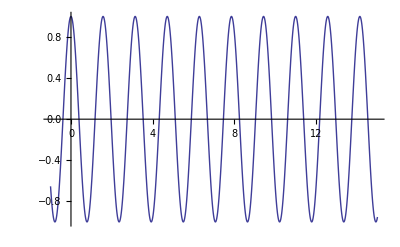

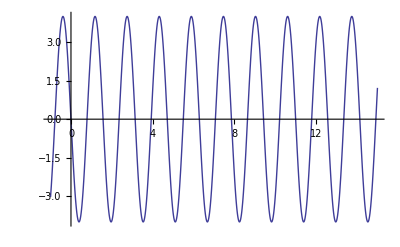

```mathematica
Plot[p[x],{x,-1,15}]
Plot[dp[x],{x,-1,15}]
```

```mathematica
p[xx_]:=Exp[-xx/10]*Cos[xx]+1/10*xx
```

```mathematica
dp[xx_]=D[p[xx],xx]
```

1/10-1/10 ⅇ^(-xx/10) Cos[xx]-ⅇ^(-xx/10) Sin[xx]

```mathematica
dp[Pi]
```

1/10+ⅇ^(-π/10)/10

```mathematica
p[x]
```

x/10+ⅇ^(-x/10) Cos[x]

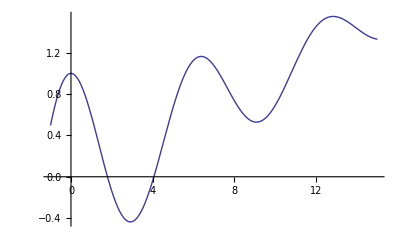

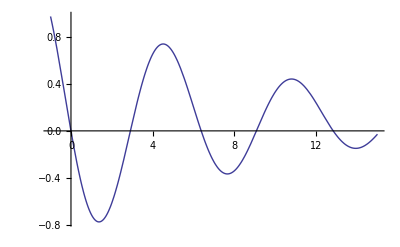

```mathematica
Plot[p[x],{x,-1,15}]
Plot[dp[x],{x,-1,15}]
```

```mathematica
FindRoot[dp[x],{x,0}]
```

{x→0.}

```mathematica
FindRoot[dp[x],{x,Pi}]
```

{x→2.90844}

```mathematica
p[2.90843618110617]
```

-0.436559

```mathematica
FindRoot[dp[x],{x,2*Pi}]
```

{x→6.37284}

```mathematica
FindRoot[dp[x],{x,3*Pi}]
```

{x→9.07593}

```mathematica
p[9.075933682494183]
```

0.528402

```mathematica
FindRoot[dp[x],{x,4*Pi}]
```

{x→12.834}

```mathematica
FindRoot[dp[x],{x,5*Pi}]
```

{x→15.1391}